Министерство образования и науки Российской Федерации
Федеральное государственное бюджетное образовательное учреждение
высшего профессионального образования
«Национальный исследовательский Томский политехнический университет»

Институт: ИЯТШ
Отделение прикладной математики и информатики

ОТЧЕТ ПО ЛАБОРАТОРНОЙ РАБОТЕ №4
 Волновое уравнение: аналитическое решение методами Фурье и Даламбера, численное решение
Вариант №2

Выполнил: студент группы 0В01
Белясов Архип
Проверил: Богданов О.В.

Задание
	Дана струна длины L=π, закрепленная на концах. Начальное смещение u[x,0]==Sinh[x/π](π-x)^2 . Начальная скорость и внешние силы равны нулю, волновой параметр а взять равным 1. Получить аналитическое решение в виде ряда (Метод Фурье).

Решение

А) Исследовать профиль струны, используя построенное методом Фурье аналитическое решение, в зависимости от индекса суммирования (n=1, 2,...,5,...,15, и т.д.). Исследовать ряд на сходимость: подобрать такое n оптимальное когда профиль струны уже не будет визуально меняться при дальнейшем увеличении n.

Зададим начальные параметры:

```mathematica
eqn=D[u[x,t],{t,2}]==D[u[x,t],{x,2}];
bc={u[0,t]==0,u[π,t]==0};
ic = {u[x,0]==Sinh[x/π](π-x)^2,Derivative[0,1][u][x,0]==0};
```

Решим волновое уравнение с заданными условиями с помощью функции DSolveValue

```mathematica
dsol=DSolveValue[{eqn,bc,ic},u[x,t],{x,t}]/.{K[1]->m}
```

(4 m π^3 Cos[m t] Sin[m x] (2-3 (-1)^m Sinh[1]+m^2 π^2 (2+(-1)^m Sinh[1])))/((1+m^2 π^2)^3)m1∞

```mathematica
sol[x_,t_] = dsol/.{∞->6}//Activate
```

(4 π^3 Cos[t] Sin[x] (2+π^2 (2-Sinh[1])+3 Sinh[1]))/((1+π^2)^3)+(12 π^3 Cos[3 t] Sin[3 x] (2+9 π^2 (2-Sinh[1])+3 Sinh[1]))/((1+9 π^2)^3)+(20 π^3 Cos[5 t] Sin[5 x] (2+25 π^2 (2-Sinh[1])+3 Sinh[1]))/((1+25 π^2)^3)+(8 π^3 Cos[2 t] Sin[2 x] (2-3 Sinh[1]+4 π^2 (2+Sinh[1])))/((1+4 π^2)^3)+(16 π^3 Cos[4 t] Sin[4 x] (2-3 Sinh[1]+16 π^2 (2+Sinh[1])))/((1+16 π^2)^3)+(24 π^3 Cos[6 t] Sin[6 x] (2-3 Sinh[1]+36 π^2 (2+Sinh[1])))/((1+36 π^2)^3)

```mathematica
Animate[Plot[sol[x,t],{x,0,π},PerformanceGoal->"Quality",PlotRange->All,ImageSize->Medium, PlotLabel->t,Frame->True,GridLines->Automatic],{t,0,12},SaveDefinitions->True]
```

Получим численное решение волнового уравнения с помощью функции NDSolveValue[]

```mathematica
usol=NDSolveValue[{eqn,bc,ic},u, {x,0,π},{t,0,12},Method->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->1000}}]
```

InterpolatingFunction[{{0., 3.14159}, {0., 12.}}, <>]

Построим трехмерный график в зависимости от x и t .

```mathematica
Plot3D[usol[x,t], {t,0,12},{x,0,π},PlotRange->All]
```

-Graphics3D-

В) Исследовать профиль струны методом Даламбера. Сравнить с пунктами А и Б.

```mathematica
a=1;L=π;
stc[x_,w_]=Abs[x-w Floor[x/w+1/2]];
```

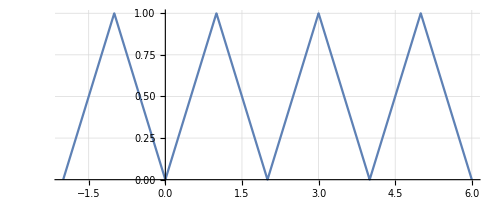

```mathematica
Plot[stc[x,2],{x,-2,6},AspectRatio->Automatic,Exclusions->None,GridLines->Automatic]
```

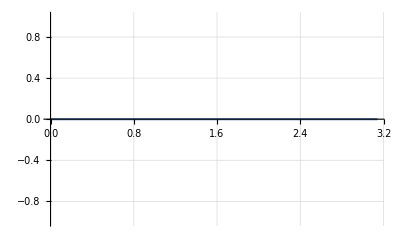

```mathematica
ψ[x_]=0;
Plot[ψ[x],{x,0,π},Exclusions->None,GridLines->Automatic]
```

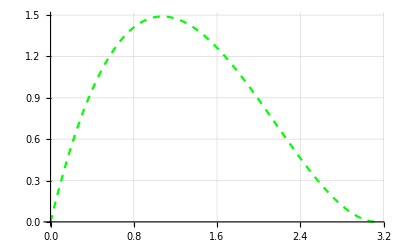

```mathematica
ϕ[x_]=Sinh[x/π](π-x)^2;
Plot[ϕ[x],{x,0,π},Exclusions->None, PlotStyle->{Dashed, Green},GridLines->Automatic]
```